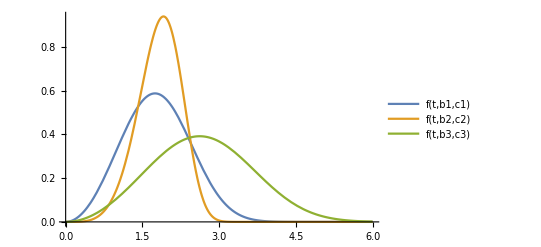

```mathematica
Clear[b1,c1,b2,c2,b3,c3,b4,c4,f,b,c,t];
b1=3; b2=5; b3=3; 
c1=2; c2=2; c3=3;
(*1.1 Функция плотности распределения Вейбулла f(t) *)
f[t_,b_,c_] := b/c(t/c)^(b-1)*E^(-(t/c)^b);
(* построение графика плотности распределения *)
Plot[{f[t,b1,c1],f[t,b2,c2],f[t,b3,c3]},{t,0,6},PlotLegends->"Expressions"]
```

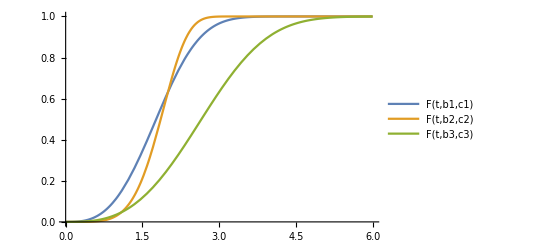

```mathematica
(* 1.2 Функция распределения Вейбулла F(t) *)
Clear[F,t,b,c];
F[t_,b_,c_] := 1-E^(-(t/c)^b);
(* построение графика распределения *)
Plot[{F[t,b1,c1],F[t,b2,c2],F[t,b3,c3]},{t,0,6},PlotLegends->"Expressions"]
```

```mathematica
(* 1.3 Математическое ожидание, Дисперсия, Среднеквадратическое отклонение*)
Clear[α1,α2,α3,M1,M2];
α1[b_,c_]:=Integrate[t*f[t,b,c],{t,0,Infinity}];          (*Первый начальный момент*)
α2[b_,c_]:=Integrate[t^2*f[t,b,c],{t,0,Infinity}];     (*Второй начальный момент*)
(* Математическое ожидание ( 1-ый начальный момент ) *)
M1:=α1 ;
N[M1[b1,c1]]
N[M1[b2,c2]]
N[M1[b3,c3]]
```

1.78596

1.83634

2.67894

```mathematica
(* Дисперсия *)
Clear[D1,D2];
D1[b_,c_]:=α2[b,c]-(α1[b,c])^2;
N[D1[b1,c1]]
N[D1[b2,c2]]
N[D1[b3,c3]]
```

0.421332

0.17692

0.947996

```mathematica
(* СКО *)
Clear[σ,μ3,S];
σ[b_,c_]:=Sqrt[D1[b,c]];
N[σ[b1,c1]]
N[σ[b2,c2]]
N[σ[b3,c3]]
```

0.649101

0.420618

0.973651

```mathematica
(* 2.1  Построение генератора случайных величин наработок до отказа объектов, распределенных закону Вейбулла*)
Clear[n,a,b,i,Y1,X11,X12,X13,X21,X22,X23];
n=10000;
a = 0; b=1;
Y1=RandomReal[b,n];
X11={};X12 ={}; X13={};
For[i=1,i≤n,i++,AppendTo[X11,-c1*Surd[Log[1-Part[Y1,i]],b1]]];
For[i=1,i≤n,i++,AppendTo[X12,-c2*Surd[Log[1-Part[Y1,i]],b2]]];
For[i=1,i≤n,i++,AppendTo[X13,-c3*Surd[Log[1-Part[Y1,i]],b3]]];
X21=Sort[X11];
X22=Sort[X12];
X23=Sort[X13];
ListPlot[{Labeled[X21,"X21"],Labeled[X22,"X22"],Labeled[X23,"X23"]},PlotStyle->PointSize[Small]]
```

-Graphics-

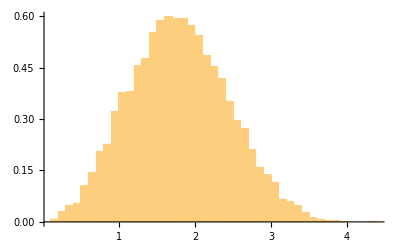

```mathematica
(*2.2 Построение гистограмм распределения случаных величин*)
Clear[bin,lower,upper,h,int,j];
bin = 40;
lower = Floor[Min[X11]];
upper = Ceiling[Max[X11]];

h = (upper -lower)/n;
For[j=1 ; int = 0,j≤bin+1,j++,int = lower + h*j];
Histogram[X11,bin,"PDF"]
```

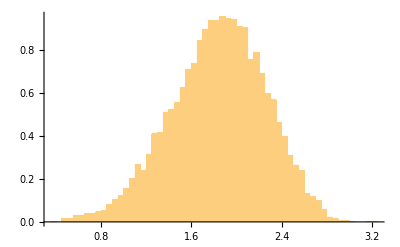

```mathematica
Clear[lower,upper,h,int,j];
lower = Floor[Min[X12]];
upper = Ceiling[Max[X12]];

h= (upper -lower)/n;
For[j=1 ; int = 0,j≤bin+1,j++,int = lower + h*j];
Histogram[X12,bin,"PDF"]
```

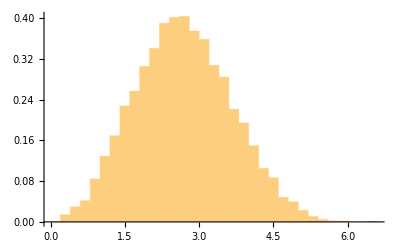

```mathematica
Clear[lower,upper,h,int,j];
lower = Floor[Min[X13]];
upper = Ceiling[Max[X13]];

h= (upper -lower)/n;
For[j=1 ; int= 0,j≤bin+1,j++,int= lower + h*j];
Histogram[X13,bin,"PDF"]
```

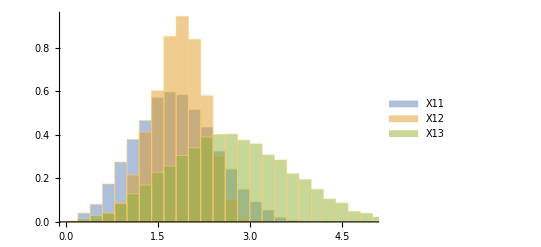

```mathematica
Histogram[{X11,X12,X13},bin,"PDF",ChartLegends->{"X11","X12","X13"}, ChartStyle->{RGBColor[0.368417,0.506779,0.709798],RGBColor[0.880722,0.611041,0.142051],RGBColor[0.560181,0.691569,0.194885]}]
```

```mathematica
(*3 Получение числовых оценок случайной величины в виде математического ожидания и дисперсии*)
Clear[m1,m2,m3];
m1 =Total[X11]/n
m2=Total[X12]/n
m3=Total[X13]/n
```

1.78924

1.83898

2.68387

```mathematica
Clear[j,X1,X2,X3,d1,d2,d3];
X1={};X2={};X3={};
For[j=1 ,j≤n,j++,AppendTo[X1,Part[X11,j]^2]];
For[j=1 ,j≤n,j++,AppendTo[X2,Part[X12,j]^2]];
For[j=1 ,j≤n,j++,AppendTo[X3,Part[X13,j]^2]];
d1=(Total[X1] /n)- m1^2
d2=(Total[X2] /n)- m2^2
d3=(Total[X3] /n)- m3^2
```

0.414698

0.173957

0.933071

```mathematica
△m1=Abs[M1[b1,c1]-m1]
△m2=Abs[M1[b2,c2]-m2]
△m3=Abs[M1[b3,c3]-m3]
```

0.00328478

0.00264344

0.00492717

```mathematica
△d1=Abs[D1[b1,c1]-d1]
△d2=Abs[D1[b2,c2]-d2]
△d3=Abs[D1[b3,c3]-d3]
```

0.00663337

0.00296262

0.0149251